```mathematica
TEM23
```

X-Richtung:

{μ→421.674,σ→77.7091,k→1162.62}

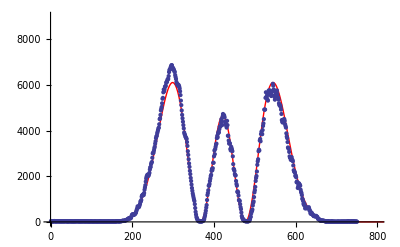

Y-Richtung:

{μ→248.956,σ→85.9621,k→224.818}

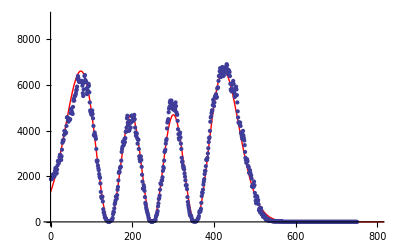

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM23.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 2;
yKnoten = 3;

Clear @ model;
model[x_] = k*Exp[- ((x-μ)/σ)^2]*HermiteH[n, (x-μ)/σ]^2;Print["X-Richtung:"];

param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 400}, {σ, 50}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 300}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
```

```mathematica
TEM33
```

X-Richtung:

{μ→442.4,σ→78.7475,k→68.7467}

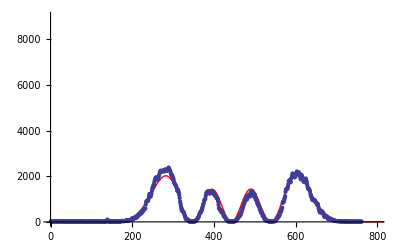

Y-Richtung:

{μ→244.328,σ→84.807,k→91.7463}

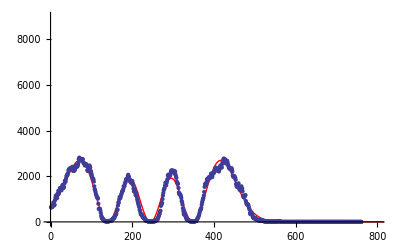

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM33.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 3;
yKnoten = 3;

Clear @ model;
model[x_] = k*Exp[- ((x-μ)/σ)^2]*HermiteH[n, (x-μ)/σ]^2;Print["X-Richtung:"];

param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 500}, {σ, 80}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 300}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
```

```mathematica
TEM50
```

X-Richtung:

{μ→440.895,σ→80.112,k→1.4719}

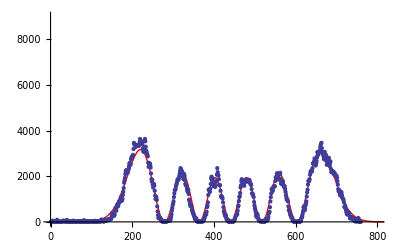

Y-Richtung:

{μ→231.669,σ→84.4827,k→3597.15}

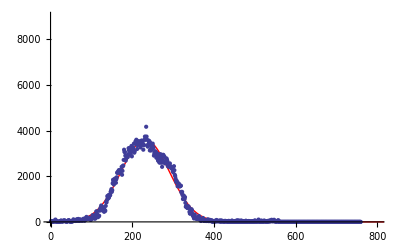

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM50.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 5;
yKnoten = 0;

Clear @ model;
model[x_] = k*Exp[- ((x-μ)/σ)^2]*HermiteH[n, (x-μ)/σ]^2;Print["X-Richtung:"];

param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 400}, {σ, 80}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 300}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
```

```mathematica
TEM52
```

X-Richtung:

{μ→419.064,σ→75.4268,k→444.784}

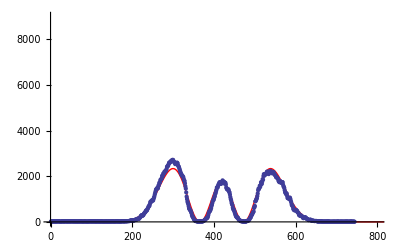

Y-Richtung:

{μ→252.043,σ→86.0702,k→1.02425}

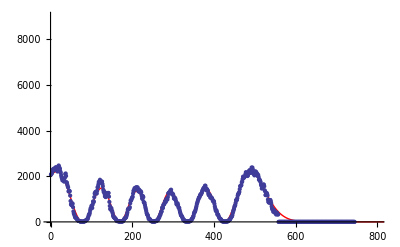

```mathematica
rawData = Import[NotebookDirectory[]<>"TEM25.dat"];
messData  = ToExpression[rawData];
xData = Map[First, messData];
yData = Map[Last, messData];

xKnoten = 2;
yKnoten = 5;

Clear @ model;
model[x_] = k*Exp[- ((x-μ)/σ)^2]*HermiteH[n, (x-μ)/σ]^2;Print["X-Richtung:"];

param=FindFit[xData, model[x] /. {n->xKnoten}, {{μ, 400}, {σ, 50}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->xKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[xData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]

Print["Y-Richtung:"];

param=FindFit[yData, model[x]/. {n->yKnoten}, {{μ, 250}, {σ, 100}, {k, 1000}}, x]
thPlot = Plot[ model[x]/.Join[param, {n->yKnoten}],  {x,0,9000}, PlotStyle->Red, PlotRange->{{0, 800},{0, 9000}}];
realPlot = ListPlot[yData, PlotRange->{{0,800}, {0, 9000}}];
Show[{thPlot, realPlot}]
```